Detecting Entities in the Enchanted Forest Plain Text
Ian Milligan - 30 May 2019

Let’s start by importing the derivative file (using 10,000 websites as a starting point).

```mathematica
eftext = Import["/users/ianmilligan1/dropbox/git/geocities/10000lines.txt","Lines"];
```

Now let’s use a map function to extract just the plain text. StringSplit[] effectively splits on the first five commas, and the fifth element is just the HTML response of the web archive. We then go through that for as many records as there are.

```mathematica
text = StringSplit[eftext⟦#⟧,",",5]⟦5⟧&/@Range[Length[eftext]];
```

Now we want to run various classifiers.

Dates

```mathematica
interpretdates=TextCases[text,"Date"->"Interpretation",PerformanceGoal->"Speed"];
```

```mathematica
dates=Flatten[interpretdates];
```

```mathematica
Length[dates]
```

48241

```mathematica
years=DateObject[dates⟦#⟧,"Year"]&/@Range[Length[dates]];
```

```mathematica
flatyears=Flatten[years]
```

{Year: 2009,Year: 2009,Year: 2009,Year: 1998,Year: 1997,Year: 1996,Year: 1995,Year: 1994,Year: 1993,Year: 1992,Year: 1991,Year: 1990,Year: 1989,Year: 1988,48213,Year: 2009,Year: 1999,Year: 1735,Year: 2009,Year: 1997,Year: 2009,Year: 1997,Year: 2009,Year: 1999,Year: 2009,Year: 2009,Year: 2009,Year: 2009,Year: 2003}
 |  |  |  |

```mathematica
yearstring=DateString/@flatyears;
```

```mathematica
freq=Take[Sort[Tally[yearstring],Greater],40]
```

{{2009,16632},{1998,7301},{1997,2612},{1996,402},{1995,180},{1994,124},{1993,83},{1992,81},{1991,70},{1990,129},{1989,44},{1988,61},{1987,43},{1986,49},{1985,42},{1984,53},{1983,36},{2008,305},{2002,633},{2003,3136},{1780,4},{2016,2},{2004,169},{1795,6},{2019,2287},{1999,6878},{2000,1491},{1982,39},{2007,167},{2001,1165},{1700,14},{1921,11},{1846,7},{1857,5},{2005,194},{1836,5},{1957,16},{1920,35},{2006,107},{1825,13}}

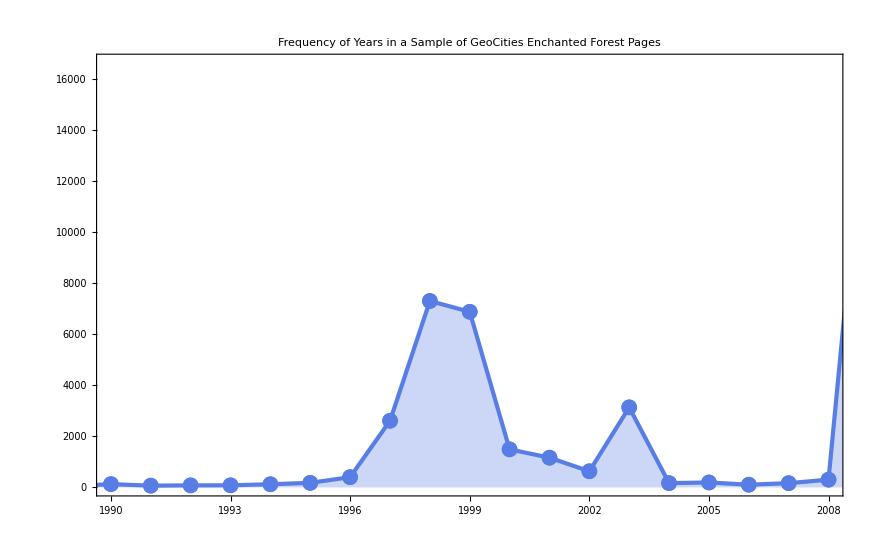

```mathematica
DateListPlot[freq,PlotTheme->"Business",PlotRange->{{{1990},{2008}},All},PlotMarkers->"OpenMarkers",GridLines->Automatic,Filling->Axis,Mesh->Full,FrameTicks->{Automatic,{{{1990,1,1},{1991,1,1},{1992,1,1},{1993,1,1},{1994,1,1},{1995,1,1},{1996,1,1},{1997,1,1},{1998,1,1},{1999,1,1},{2000,1,1},{2001,1,1},{2002,1,1},{2003,1,1},{2004,1,1},{2005,1,1},{2006,1,1},{2007,1,1},{2008,1,1},{2009,1,1},{2010,1,1},{2011,1,1},{2012,1,1},{2013,1,1},{2014,1,1},{2015,1,1},{2016,1,1}},None}},PlotLabel->"Frequency of Years in a Sample of GeoCities Enchanted Forest Pages"]
```

Locations

```mathematica
interpretlocations=TextCases[text,"Location"->"Interpretation",PerformanceGoal->"Speed"];
```